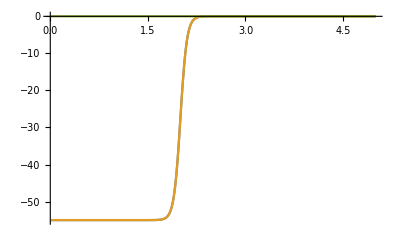

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=55;R=2;a=0.05;μ=8/9 Subscript[m, N];l=0;
rmax=5.;dr=0.01;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
Vwoods[r_]:=-V0/(1+Exp[(r-R)/a]);
Vcent[r_]:=(l(l+1)ℏc^2)/(2μ r^2);
V[r_]:=-V0/(1+Exp[(r-R)/a])+(l(l+1)ℏc^2)/(2μ r^2);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[{V[rlist],Vwoods[rlist],Vcent[rlist]},DataRange->{dr,rmax}]
```

```mathematica
(*DEFINE REQUIRED FUNCTIONS*)
```

```mathematica
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
k[En_]:=I Sqrt[(2μ En)/ℏc^2];
wave[En_,r_,δ_,l_]:=1/2 Exp[I δ](Cos[δ]SphericalBesselJ[l,k[En] r]-Sin[δ] SphericalBesselY[l,k[En] r]);
B[En_,δ_,l_]:=k[En] rmax(((Cos[δ] D[SphericalBesselJ[l,x], x]/.x->k[En] rmax)-(Sin[δ] D[SphericalBesselY[l,x], x]/.x->k[En] rmax))/(Cos[δ]SphericalBesselJ[l,k[En] rmax]-Sin[δ]SphericalBesselY[l,k[En] rmax]));
Hnew[En_,δ_,l_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr B[En,δ,l]/rmax-1);H);
eigenv[{En_,i_,δ_,l_}]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnew[En,δ,l]]],First];{eval[[i]],δ});
findnd[En_]:=Module[{phase=List[],n=1},(While[Max[Table[eigenv[{En,n,δ,l}][[1]],{δ,0.,π,0.1}]]<En,n++;];phase=Table[{eigenv[{En,n,δ,l}][[1]],δ},{δ,0,π,0.01}];δ=phase[[Position[phase[[All,1]],Nearest[phase[[All,1]],En][[1]]][[1,1]],2]];{n,δ})]
const[i_]:=Re[evec[[i,-1]]]/Re[wave[eval[[i]],rmax,δ,l]]
wvplot[En_]:=Module[{n=findnd[En][[1]],δ=findnd[En][[2]]},{eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnew[En,δ,l]]],First];Print[{En,eval[[n]],n,δ}];ListLinePlot[{Transpose[{rlist,evec⟦n⟧}],Transpose[{Range[rmax,rmaxx,dr],Re[const[n] wave[eval[[n]],Range[rmax,rmaxx,dr],δ,l]]}]},PlotRange->All]]
```

{-24.3086,-24.3116+0. ⅈ,1,1.12}

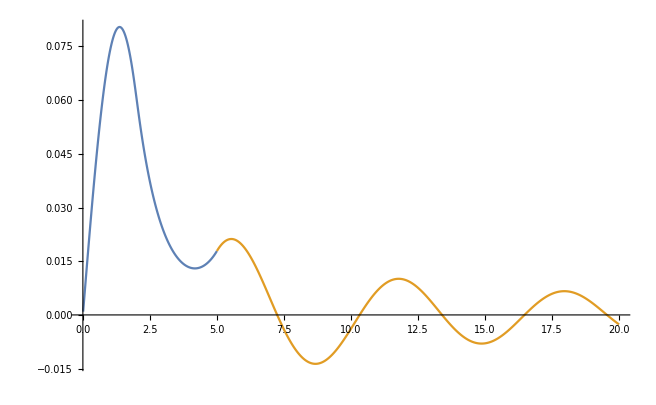
{130.776,-Graphics-}

```mathematica
rmaxx=20.;
wvplot[-24.3086]//Timing
```